```mathematica
What do systems look like at different densities (and perhaps other parameters)?
How many tries did it take to do this?
What does the structure function look like (positional and orientational?
```

```mathematica
createCircle[r_, boxX_ , boxY_]:={{boxX*Random[], boxY*Random[]}, r}
```

```mathematica
circleIntersectQ[{{x1_, y1_}, r1_},{{x2_, y2_}, r2_} ]:=If[Sqrt[(x1-x2)^2+(y1-y2)^2]<r1+r2, True, False]
```

```mathematica
distance[{{x1_, y1_}, r1_},{{x2_, y2_}, r2_}]:=Sqrt[(x1-x2)^2+(y1-y2)^2]
```

```mathematica
Print[uu];
circles={};
newCircle=createCircle[0.1, 10, 10];
circle=Append[circles, newCircle];
For[i=1,i<500, i++,
newCircle=createCircle[0.1, 10, 10];
intersect=MemberQ[Complement[circleIntersectQ[newCircle, #]&/@circles], True];
circles=If[intersect, circles, Append[circles,newCircle]];];
```

uu

```mathematica
Disk[circles[[55]]]
```

Disk[{{2.84465,6.56641},0.1}]

```mathematica
i=99;
```

```mathematica
closestNeighbor=Sort[{#, distance[circles[[99]],#]}&/@circles, #1[[2]] < #2[[2]] &][[2]]
```

{{{7.53075,1.39959},0.1},0.371869}

```mathematica
xq[x1_, x2_, a_]:=(a*x1 + (2-a)*x2)/2
```

```mathematica
yq[y1_, y2_, a_]:=(a*y1 + (2-a)*y2)/2
```

```mathematica
Dist[x1_, y1_, x2_, y2_, a_]:=Sqrt[(x1-xq[x1, x2, a])^2+(y1-yq[y1, y2, a])^2]
```

```mathematica
{x1, y1}
```

{2.46826,4.49981}

```mathematica
{x2, y2}
```

{2.33579,4.34997}

```mathematica
alpha
```

{}⟦1⟧

```mathematica
(* This approach doesn't work because everyone already has a neighbor that the
```

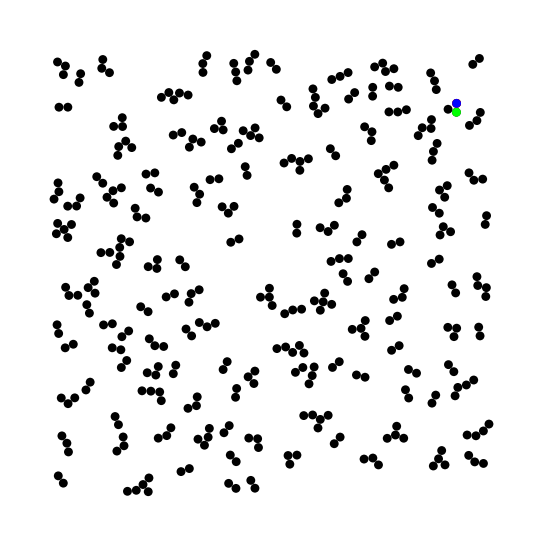
Null -Graphics-

```mathematica
For[j=1, j<10000, j++, element=Round[(Length[circles]-1)*Random[]+1];
item=circles[[element]];
closestNeighbor=Sort[{#, distance[item,#]}&/@circles, #1[[2]] < #2[[2]] &][[2]];
{x1, y1}=closestNeighbor[[1]][[1]];
{x2, y2}=item[[1]];
alpha=Select[z/.NSolve[Dist[x1, y1, x2, y2, z]==0.2, z], #> 0 && # < 2&];
circles[[element]]=If[Length[alpha]≥1, 
{{(alpha[[1]]*x1+(2-alpha[[1]])*x2)/2, (alpha[[1]]*y1+(2-alpha[[1]])*y2)/2}, 0.1}, circles[[element]]];]Graphics[{Disk[#[[1]], #[[2]]]&/@circles, Red, Disk[item[[1]], item[[2]]], Green, Disk[closestNeighbor[[1]][[1]], closestNeighbor[[1]][[2]]], Blue, Disk[circles[[element]][[1]], circles[[element]][[2]]]}]
```

```mathematica
For[j=1, j<500, j++,
element=Round[(Length[circles]-1)*Random[]+1];
item=circles[[element]];
closestNeighbor=Sort[{#, distance[item,#]}&/@circles, #1[[2]] < #2[[2]] &][[2]];
{x1, y1}=closestNeighbor[[1]][[1]];
{x2, y2}=item[[1]];
alpha=Select[z/.NSolve[Dist[x1, y1, x2, y2, z]==0.2, z], #> 0 && # < 2&][[1]];
circles[[element]]={{(alpha*x1+(2-alpha)*x2)/2, (alpha*y1+(2-alpha)*y2)/2}, 0.1};]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

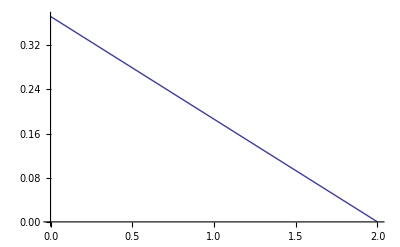

{{{7.36805,0.346628},0.1},0.309781}

```mathematica
ListPlot[{#,Dist[#]}&/@Range[0,2,0.1], Joined->True]
```